# Pure shear

## preliminary data

### load data

```mathematica
p0s={3.825}
```

{3.825}

```mathematica
temperatures={{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015}};
 records={{10}};
epsilons={{-0.01,0.,0.01},{-0.0001,0.,0.0001}};
tauEstimate={{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
pureShearDerivatives=Table[Table[
Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/pureShear/p","/pureShearDerivatives1st2nd_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timeEnergy=Table[Table[
Table[Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/pureShear/p","/timeEnergy_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

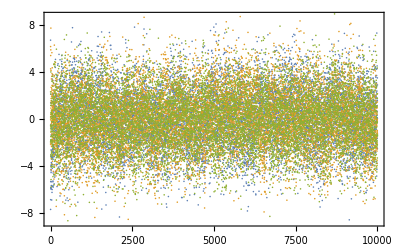

```mathematica
ListPlot[{Table[{timeEnergy[[1,12,1,1,1,1,i]],pureShearDerivatives[[1,12,1,1,1,1,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],pureShearDerivatives[[1,12,1,3,1,1,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],pureShearDerivatives[[1,12,1,2,1,1,i]]},{i,10000}]}]
```

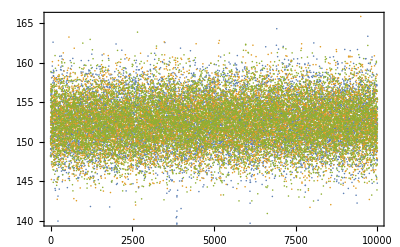

```mathematica
ListPlot[{Table[{timeEnergy[[1,12,1,1,1,1,i]],timeEnergy[[1,1,1,1,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],timeEnergy[[1,1,1,3,1,2,i]]},{i,10000}],Table[{timeEnergy[[1,12,1,3,1,1,i]],timeEnergy[[1,1,1,2,1,2,i]]},{i,10000}]}]
```

```mathematica
Dimensions[timeEnergy]
```

{1,1,2,3,1}

```mathematica
g1=Table[Table[
Table[Table[Mean[Normal[pureShearDerivatives[[p,T,ep,2,rec,2]]]],{rec,Length[records[[p]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
g1*0.05^2
```

{{{{27.0948},{27.0948}},{{21.7683},{21.7683}},{{19.5711},{19.5711}},{{14.4179},{14.4179}},{{11.7389},{11.7389}},{{10.719},{10.719}},{{9.7994},{9.7994}},{{9.05463},{9.05463}},{{8.34697},{8.34697}},{{7.88169},{7.88169}},{{7.50981},{7.50981}},{{7.18712},{7.18712}},{{6.87369},{6.87369}}}}